## section1

### basic

```mathematica
4+555
```

559

```mathematica
3+5/3-2/5
```

64/15

```mathematica
N[π,26]
```

3.1415926535897932384626434

```mathematica
Head[{3}]
```

List

```mathematica
{2+2ⅈ}*{5+5/3ⅈ}
```

{20/3+(40 ⅈ)/3}

### Functions

```mathematica
Plus[2,669.5,"ddsd"]
```

671.5+ddsd

```mathematica
Times[9,Plus[2,3]]
```

45

```mathematica
Head[4^3]
```

Integer

```mathematica
4^5+27^(1/3)
```

1027

```mathematica
Max[25,36,5^7,"hahha"]
```

Max[78125,hahha]

```mathematica
Max[351,5,5^7]
```

78125

```mathematica
Max["hello","yes","hahahhahah"]
```

Max[hahahhahah,hello,yes]

```mathematica
Rotate["hahahaha",π/3]
```

hahahaha

```mathematica
Image@RandomInteger[1,{128,128}]
```

-Graphics-

### Lists

```mathematica
Plus[3,5,6]
```

14

```mathematica
Head@{1,2,3,4,a,b,c}
```

List

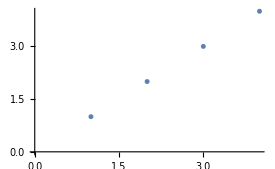

```mathematica
ListPlot[{1,2,3,4,a,b,c}]
```

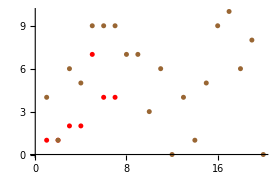

```mathematica
ListPlot[{{1,1,2,2,7,4,4},RandomInteger[10,20]},PlotStyle->{Red,Brown}]
```

```mathematica
Range[1,20,2/3]
```

{1,5/3,7/3,3,11/3,13/3,5,17/3,19/3,7,23/3,25/3,9,29/3,31/3,11,35/3,37/3,13,41/3,43/3,15,47/3,49/3,17,53/3,55/3,19,59/3}

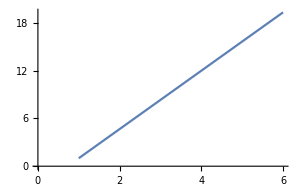

```mathematica
ListLinePlot@Range[1,20,11/3]
```

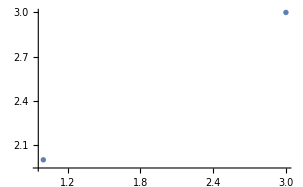

```mathematica
ListPlot@Reverse[{{1,2},{3,3}}]
```

```mathematica
Join[{3,2+5,1},{0.5,6.7},{{"dd","da"},{2,6}}]
```

{3,7,1,0.5,6.7,{dd,da},{2,6}}

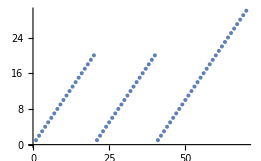

```mathematica
Rotate[ListPlot[Join[Range[20],Range[20],Range[30]]],π/8]
```

```mathematica
Counts@Join[Range[3],Range[5]]
```

<|1→2,2→2,3→2,4→1,5→1|>

```mathematica
Counts@RandomInteger[10,30]
```

<|3→4,7→3,4→4,5→4,8→3,6→3,0→4,10→1,1→2,9→1,2→1|>

```mathematica
Sort@Counts@RandomInteger[10,30]
```

<|2→1,5→2,7→2,3→2,1→3,8→3,0→4,9→4,10→4,4→5|>

```mathematica
Normal@Counts@RandomInteger[10,30]
```

{0→1,5→4,6→4,10→3,7→4,1→5,2→3,8→3,9→2,4→1}

### Displaying Lists

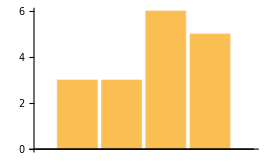

```mathematica
BarChart[{3,3,6,5}]
```

```mathematica
Column[{100,3,"asd",-Graphics-}]
```

100
3
asd
-Graphics-

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1},{1,2,1,4}},Mesh->All]
```

-Graphics3D-

```mathematica
data=Table[Sin[j^2+i],{i,0,Pi,Pi/5},{j,0,Pi,Pi/5}];
```

```mathematica
ListPlot3D[data,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

### Operations

```mathematica
{1,3,6,"haha"}+3
```

{4,6,9,3+haha}

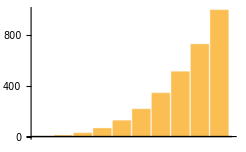

```mathematica
BarChart[Range[10]^3]
```

```mathematica
Take[Range@20,{3,10}]
```

{3,4,5,6,7,8,9,10}

```mathematica
{1,5,8,6,11}[[2;;-4]]
```

{5}

```mathematica
RotateLeft@{7,7,6,99,1}
```

{7,6,99,1,7}

```mathematica
Last[IntegerDigits[1988]]
```

8

### Table

```mathematica
Table[5,15]
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
Table[i,{i,5,10}]
```

{5,6,7,8,9,10}

```mathematica
Table[Range[n],{n,4}]
```

{{1},{1,2},{1,2,3},{1,2,3,4}}

```mathematica
PieChart@Table[Range[n],{n,4}]
```

-Graphics-

```mathematica
PieChart@Table[1,4]
```

-Graphics-

```mathematica
testData = Table[x-x^2,{x,0,1,.02}]
```

{0.,0.0196,0.0384,0.0564,0.0736,0.09,0.1056,0.1204,0.1344,0.1476,0.16,0.1716,0.1824,0.1924,0.2016,0.21,0.2176,0.2244,0.2304,0.2356,0.24,0.2436,0.2464,0.2484,0.2496,0.25,0.2496,0.2484,0.2464,0.2436,0.24,0.2356,0.2304,0.2244,0.2176,0.21,0.2016,0.1924,0.1824,0.1716,0.16,0.1476,0.1344,0.1204,0.1056,0.09,0.0736,0.0564,0.0384,0.0196,0.}

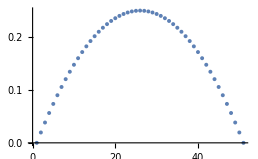

```mathematica
ListPlot[testData]
```

```mathematica
ListAnimate[Table[Plot[Sin[n x],{x,0,10}],{n,5}]]
```

```mathematica
data2D = Table[{x,y},{x,0,5,1},{y,0,5,1}];
```

```mathematica
data3D =Table[{x,y,z},{x,0,5,1},{y,0,5,1},{z,0,5,1}];
```

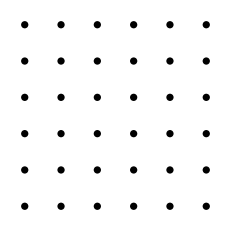

```mathematica
Graphics@Table[Disk[{x,y},.1],{x,0,5,1},{y,0,5,1}]
```

```mathematica
Graphics3D@Table[Sphere[{x,y,z},.1],{x,1,5,1},{y,3,5,1},{z,0,7,1}]
```

-Graphics3D-

### Basic Graphics

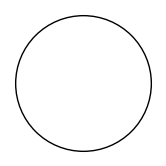

```mathematica
Graphics[Circle[]]
```

```mathematica
ImageResize[-Graphics-,{142,151}]
```

-Graphics-

```mathematica
-Graphics-+(-Graphics--0.2)
```

-Graphics-